#### A rare example of Mathematica’s NMinimize failing. GetTempAndθ0σ0ϕ0[Tmat_,Σ_] calls NMinimize and is in common_funs.nb INSTRUCTIONS: Run common_funs.nb, ChooseTmat.nb, then this notebook

#### shortest test case: with nRuns=1, minimization fails; with nRuns=2, it works

```mathematica
(*Tmat = TmatBrownAn00;
TmatTRIG=Closest[Tmat,TRIG];
TmatCUBE=Closest[Tmat,CUBE];
Tmatx=0.3TmatTRIG+0.7TmatCUBE;
nRuns=1;
Σ=MONO;
βT[Tmatx,Σ]/Degree
MinimizationFacts[Tmatx,Σ];
nRuns=2;
βT[Tmatx,Σ]/Degree
MinimizationFacts[Tmatx,Σ];*)
(*Clear[βT,dT,UT]*)
```

#### copied from ES_FindSymGroups.nb

```mathematica
(*GetTempAndθ0σ0ϕ0[Tmat_,Σ_]:=(Clear[θ,σ,ϕ];
temp[Tmat,Σ]= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],Σ],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[Tmat,Σ][[2]]);
If[MemberQ[{XISO,MONO},Σ],σ0=0];)*)
```

#### Function to minimize over a localized square patch

```mathematica
Flocal[theta0_,phi0_,dtheta_,dphi_,Tmat_]:=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],theta0-dtheta≤θ≤theta0+dtheta&&phi0-dphi≤ϕ≤phi0+dphi},{θ,ϕ},Method->"RandomSearch"];
```

#### Adjust dθ based on how close the local minima are.

```mathematica
dtheta = 0.2π;
dphi=dtheta;
```

## Get the problematic map

#### nRuns=1 to illustrate the issue (nRuns=2 will solve the issue)

```mathematica
nRuns
```

```mathematica
Tmat = TmatBrownAn00;
```

#### The problematic point is t = 0.7 on the segment from TRIG to CUBE.

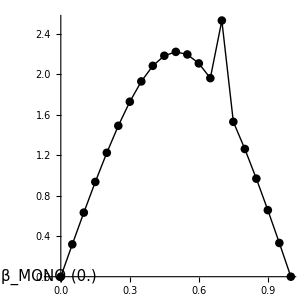

#### closest to MONO (we do not actually need this) Minimization is CORRECT

```mathematica
MinimizationFacts[Tmat,MONO]
```

```mathematica
Show[{ContourPlot[Alpha[Tmat,{θ,ϕ},MONO]/Degree,{θ,1.55,1.8},{ϕ,2.2,2.4},Contours->Automatic,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[Tmat,MONO].{0,0,1}]]}}]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

#### closest to TRIG, closest to CUBE

```mathematica
(*OutputFor[Tmat,TRIG]
OutputFor[Tmat,CUBE]*)
```

#### Reconstruct the problematic map.

```mathematica
TmatTRIG=Closest[Tmat,TRIG];
TmatCUBE=Closest[Tmat,CUBE];
Tmatx=0.3TmatTRIG+0.7TmatCUBE;
DispMat[TmatTRIG,2]
DispMat[TmatCUBE,2]
DispMat[Tmatx,2]
```

## 3D surface plot

### Plot3D gets the extremum right-- - it is the slightly redder peak. (The plot is of minus alpha_MONO.) NMinimize gets it wrong . I do not see anything pathological about the true extremum. The secondary extremum value is of course a bit close to the global extremum value, but we have to expect that sort of thing. Your multiple runs below, with different seeds, show that Mathematica is not very good at this Tmat. In general, more than one run therefore seems prudent.

```mathematica
NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,ϕ}],MONO],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"]
{θ0,σ0,ϕ0}={θ,σ,ϕ}/.%[[2]]
```

```mathematica
Show[{Plot3D[-.15Alpha[Tmatx,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},ColorFunction->(ColorData["TemperatureMap"]),Mesh->False,BoxRatios->Automatic,PlotPoints->50,PlotLegends->Automatic],
Graphics3D[{Green,Thickness[.002],
Line[{{θ0,ϕ0,-.15Alpha[Tmatx,{θ0,ϕ0},MONO]/Degree},
         {θ0,  π,-.15Alpha[Tmatx,{θ0,ϕ0},MONO]/Degree}}]}]},ImageSize->1000]
```

## Run NMinimize Global minimum: d = 8.41834, β = 1.76 Local minimum 1: d = 12.0604, β = 2.53 Local minimum 2: d = 17.9075, β = 3.76

#### The search with “RandomSearch” fails to find the global minimum (β = 2.53 vs β = 1.76):

```mathematica
(*OutputFor[Tmatx,MONO]*)
```

#### specify a number of minimizations to try

```mathematica
NTRY=10;
Σ=MONO;
```

#### With the default method, we will always get the same output – even for σ (which does not impact U):

```mathematica
Do[Print[NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->"RandomSearch"]],{5}];
```

#### Now we’ll try the RandomSeed option. RandomInteger[1] will give 0 or 1. Let’s start by fixing it to 0. This gives the same (incorrect) result always.

```mathematica
Do[Print[NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->0}]],{5}];
```

#### Now try a fixed value of 1. This gives the same (correct) result always.

```mathematica
Do[Print[NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->1}]],{5}];
```

#### Now try a random integer. Results vary, though most of the time it finds the minimum. We can list (and save) the seed integer for each run.

```mathematica
GetTempAndΘ0Σ0Φ0[Tmat_,Σ_]:=Module[{randi,result,θ0,σ0,φ0},
Clear[θ,σ,φ];
randi=RandomInteger[100000];
result=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->randi}];
{θ0,σ0,φ0}={θ,σ,φ}/. result[[2]];
(*If[MemberQ[{XISO,MONO},Σ],σ0=0];*)
{result[[1]],θ0,σ0,φ0,randi}]
```

```mathematica
Do[Print[GetTempAndΘ0Σ0Φ0[Tmatx,MONO]],{NTRY}]
```

#### Choose randi associated with three different values obtained from NMinimize:

```mathematica
randi=46073;
NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->randi}]
```

```mathematica
randi=94211;
NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->randi}]
```

```mathematica
randi=9497;
NMinimize[{DistToVΣofU[Tmatx,UsHat[{θ,σ,φ}],Σ],0<=θ<=2 Pi&&-Pi<=σ<=Pi&&0<=φ<=Pi},{θ,σ,φ},Method->{"RandomSearch","RandomSeed"->randi}]
```

## The rest is optional

#### OPTIONAL: Plot the two endpoint maps (and zoom-in on the minima). Note: Mathematica doesn’t plot where the contours are too closely spaced, even though you tell it PlotRange->All.

```mathematica
(*OutputFor[TmatTRIG,MONO]
OutputFor[TmatCUBE,MONO]*)
```

```mathematica
Show[{ContourPlot[Alpha[TmatTRIG,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->Automatic,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatTRIG,MONO].{0,0,1}]]}}]},FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

```mathematica
cons=Range[0,10,0.5];
Show[{ContourPlot[Alpha[TmatTRIG,{θ,ϕ},MONO]/Degree,{θ,4.5,4.9},{ϕ,0.5,0.9},Contours->cons,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatTRIG,MONO].{0,0,1}]]}}]},AspectRatio->Automatic,PlotRange->All,ImageSize->300]
```

```mathematica
cons=Range[0,12,2];
Show[{ContourPlot[Alpha[TmatCUBE,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->cons,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatCUBE,MONO].{0,0,1}]]}}]},FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic,PlotRange->All,ImageSize->500]
```

```mathematica
cons=Range[0,10,0.5];
Show[{ContourPlot[Alpha[TmatCUBE,{θ,ϕ},MONO]/Degree,{θ,0,0.3},{ϕ,2.3,2.6},Contours->cons,ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
Graphics[{PointSize[.015],{Green,Point[TPxyz0to2pi[UT[TmatCUBE,MONO].{0,0,1}]]}}]},AspectRatio->Automatic,PlotRange->All,ImageSize->300]
```

#### Now let’s look at Tmatx

```mathematica
Show[{ContourPlot[Alpha[Tmatx,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},
ColorFunction->(ColorData["TemperatureMap"]),PlotLegends->Automatic],
FrameTicks->{Range[0,2π,π],Range[0,π,π/2]},AspectRatio->Automatic},PlotRange->All,ImageSize->500]
```

#### CORRECT MINIMUM (β = 1.76): Upper left blue patch and its antipode region:

```mathematica
Flocal[0.5π,0.75π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.3π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 2.53): Blue patch on the equator and its antipode region:

```mathematica
Flocal[0.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(* Flocal[1.5π,0.5π,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree *)
```

#### INCORRECT MINIMUM (β = 3.76): Blue patch at lower left and its antipode region:

```mathematica
Flocal[0,0.9,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree
(*Flocal[π,2.24,dtheta,dphi,Tmatx]
ArcSin[%[[1]]/NormMatrix[Tmatx]]/Degree*)
```

#### More detailed plot of the contours (hover the mouse over any contour)

```mathematica
ContourPlot[Alpha[Tmatx,{θ,ϕ},MONO]/Degree,{θ,0,2π},{ϕ,0,π},Contours->Range[2,8],PlotPoints->20,ContourShading->None,AspectRatio->Automatic,ImageSize->700]
```